# Regression and Other Stories

## Chapter 1.

```mathematica
hibbs=SemanticImport[FileNameJoin[{$UserDocumentsDirectory, "hibbs.csv"}], Automatic,"Dataset", HeaderLines->1, Delimiters->","]
```

```mathematica
growth := hibbs[All, "growth"]//Normal
vote := hibbs[All, "inc.party.vote"]//Normal
data := Transpose[{growth, vote}]
```

```mathematica
(*incumbant.party.vote as a function of growth*)
glm = GeneralizedLinearModelFit[data,x,x, ExponentialFamily->"Gaussian"];
```

The values 46.2476 and 3.0 are the coefficients in the fitted line y = 46.2476 + 3.0 x

```mathematica
Normal[glm]
```

46.2476+3.06053 x

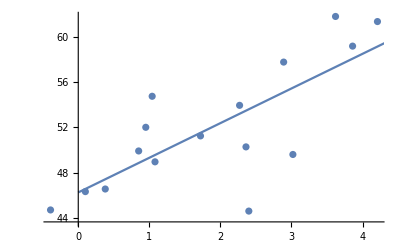

```mathematica
Show[ListPlot[data],Plot[glm[x],{x,0,8}]]
```

```mathematica
glm["ParameterTable"]
```

| Estimate | Standard Error | z-Statistic | P-Value
1 | 46.2476 | 1.62193 | 28.5139 | 7.8699×10^-179
x | 3.06053 | 0.696274 | 4.39558 | 0.0000110477

Sigma is the Residual Standard Deviation

```mathematica
StandardDeviation[glm["FitResiduals"]]
```

3.63568

## Exercises

## 1.8

### 1.1